```mathematica
Exp[1]*1.
```

2.71828

```mathematica
(40/20)^(3/2)*1.
```

2.82843

```mathematica
(40/20)^(3/2)*0.09
```

0.254558

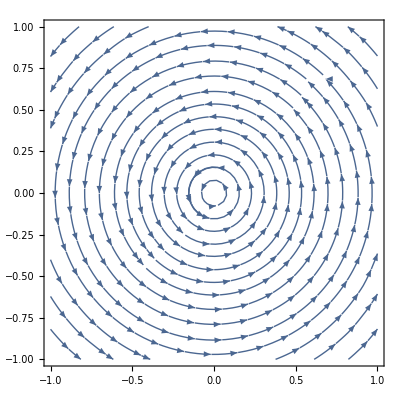

```mathematica
α=0;V[x_,y_]=ArcTan[((1-α)y)/((1+α)x)];
Xa[x_,y_]=D[V[x,y],x];Xb[x_,y_]=D[V[x,y],y];
StreamPlot[{Xa[x,y],Xb[x,y]},{x,-1,1},{y,-1,1}]
```

```mathematica
FR[x_,y_,z_,t_]=x^2+y^2-1;FI[x_,y_,z_,t_]=2(-z+t);
```

```mathematica
V[x_,y_,z_,t_]=ArcTan[FI[x,y,z,t]/FR[x,y,z,t]];
Xx[x_,y_,z_,t_]=D[V[x,y,z,t],x];Xy[x_,y_,z_,t_]=D[V[x,y,z,t],y]
Xz[x_,y_,z_,t_]=D[V[x,y,z,t],z];
```

-(4 y (t-z))/((-1+x^2+y^2)^2 (1+(4 (t-z)^2)/((-1+x^2+y^2)^2)))

```mathematica
Manipulate[StreamPlot[{Xx[x,y,0,t],Xy[x,y,0,t]},{x,-1,1},{y,-2,2}],{t,0,20}]
```